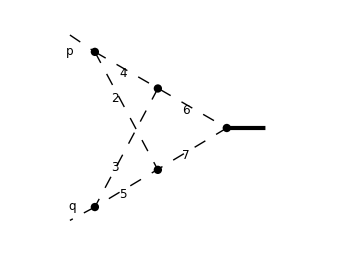
-Graphics-
(*The first entry in the basis, see below, is the irreducible numerator*)

```mathematica
(* diagram comes from the LiteRed package*)
```

```mathematica
(*generate a start file*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
Internal= {l,r};
External= {p,q};
Propagators=(- Power[##,2])&/@{l-r,l,r,p-l,q-r,p-l+r,q-r+l};
Replacements= {p^2->0,q^2->0,p q->-1/2};
PrepareIBP[];
Prepare[];
SaveStart["examples/v2"];
```

FIRE, version 5.9.dev

Prepared

Dimension set to 7

No symmetries

Saving initial data

```mathematica
Quit
```

```mathematica
(* reduction purely by FIRE *)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2",2];
Burn[]
```

FIRE, version 5.9.dev

Initial data loaded

True

```mathematica
F[2,{-1,1,1,1,1,1,1}]
```

EVALUATING {2,{-1,1,1,1,1,1,1}}

Working in sector 3/69: {2,{-1,1,1,1,1,1,1}}

LAPORTA STARTED: 1 integrals for evaluation

Maximal levels: {{0,1}}

{1,1}

Preparing points, symmetries and 104 IBP's: 0.088258 seconds.

MEMORY INFORMATION: 100 MEGABYTES REACHED

76 new relations produced: 0.622474 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,1,1,1,1}}

Sector complete

Working in sector 9/69: {2,{-1,1,1,1,1,1,-1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 131 IBP's: 0.10894 seconds.

16 new relations produced: 0.086917 seconds.

Sector complete

Working in sector 11/69: {2,{-1,-1,1,1,1,1,1}}

LAPORTA STARTED: 9 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 134 IBP's: 0.15991 seconds.

67 new relations produced: 0.646713 seconds.

Sector complete

Working in sector 13/69: {2,{-1,1,-1,1,1,1,1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 136 IBP's: 0.11589 seconds.

40 new relations produced: 0.366911 seconds.

Sector complete

Working in sector 16/69: {2,{-1,1,1,-1,1,1,1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 136 IBP's: 0.11623 seconds.

18 new relations produced: 0.089345 seconds.

Sector complete

Working in sector 20/69: {2,{-1,1,1,1,-1,1,1}}

LAPORTA STARTED: 3 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 134 IBP's: 0.06436 seconds.

53 new relations produced: 0.22407 seconds.

Sector complete

Working in sector 30/69: {2,{-1,-1,1,1,1,1,-1}}

LAPORTA STARTED: 15 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 146 IBP's: 0.077393 seconds.

94 new relations produced: 0.471038 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.09976 seconds.

122 new relations produced: 0.810641 seconds.

{2,1}

Preparing points, symmetries and 264 IBP's: 0.13794 seconds.

23 new relations produced: 0.16196 seconds.

Sector complete

Working in sector 31/69: {2,{-1,1,-1,1,1,1,-1}}

LAPORTA STARTED: 16 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.078785 seconds.

119 new relations produced: 0.531828 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.089723 seconds.

135 new relations produced: 0.744912 seconds.

{2,1}

Preparing points, symmetries and 268 IBP's: 0.12805 seconds.

60 new relations produced: 0.23276 seconds.

Sector complete

Working in sector 33/69: {2,{-1,-1,-1,1,1,1,1}}

LAPORTA STARTED: 21 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.071053 seconds.

121 new relations produced: 0.869008 seconds.

{1,2}

Preparing points, symmetries and 213 IBP's: 0.079731 seconds.

140 new relations produced: 1.4441 seconds.

{2,1}

Preparing points, symmetries and 280 IBP's: 0.12294 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,0,0,1,1,1,1}}

65 new relations produced: 0.384744 seconds.

Sector complete

Working in sector 34/69: {2,{-1,1,1,-1,1,1,-1}}

LAPORTA STARTED: 11 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.08025 seconds.

107 new relations produced: 0.460241 seconds.

Sector complete

Working in sector 36/69: {2,{-1,-1,1,-1,1,1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.080088 seconds.

57 new relations produced: 0.23752 seconds.

Sector complete

Working in sector 38/69: {2,{-1,1,-1,-1,1,1,1}}

LAPORTA STARTED: 10 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 152 IBP's: 0.072622 seconds.

62 new relations produced: 0.26872 seconds.

Sector complete

Working in sector 39/69: {2,{-1,1,1,1,-1,1,-1}}

LAPORTA STARTED: 7 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.080349 seconds.

94 new relations produced: 0.399752 seconds.

{1,2}

Preparing points, symmetries and 206 IBP's: 0.097617 seconds.

122 new relations produced: 0.65051 seconds.

{2,1}

Preparing points, symmetries and 269 IBP's: 0.12864 seconds.

20 new relations produced: 0.055069 seconds.

Sector complete

Working in sector 41/69: {2,{-1,-1,1,1,-1,1,1}}

LAPORTA STARTED: 21 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.071145 seconds.

105 new relations produced: 0.641267 seconds.

{1,2}

Preparing points, symmetries and 213 IBP's: 0.09848 seconds.

130 new relations produced: 1.19679 seconds.

{2,1}

Preparing points, symmetries and 280 IBP's: 0.14515 seconds.

75 new relations produced: 0.38463 seconds.

Sector complete

Working in sector 43/69: {2,{-1,1,-1,1,-1,1,1}}

LAPORTA STARTED: 11 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.084246 seconds.

45 new relations produced: 0.20292 seconds.

Sector complete

Working in sector 45/69: {2,{-1,1,1,-1,-1,1,1}}

LAPORTA STARTED: 16 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.079161 seconds.

121 new relations produced: 0.695764 seconds.

{1,2}

Preparing points, symmetries and 213 IBP's: 0.080896 seconds.

140 new relations produced: 1.17942 seconds.

{2,1}

Preparing points, symmetries and 280 IBP's: 0.13222 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,0,0,1,1}}

65 new relations produced: 0.368979 seconds.

Sector complete

Working in sector 46/69: {2,{-1,1,1,1,1,-1,-1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,0}}

{1,1}

Preparing points, symmetries and 130 IBP's: 0.081098 seconds.

11 new relations produced: 0.048012 seconds.

Sector complete

Working in sector 48/69: {2,{-1,-1,1,1,1,-1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.071353 seconds.

119 new relations produced: 0.513629 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.089703 seconds.

135 new relations produced: 0.745275 seconds.

{2,1}

Preparing points, symmetries and 268 IBP's: 0.12891 seconds.

49 new relations produced: 0.1594 seconds.

Sector complete

Working in sector 50/69: {2,{-1,1,-1,1,1,-1,1}}

LAPORTA STARTED: 6 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 146 IBP's: 0.073279 seconds.

14 new relations produced: 0.058582 seconds.

Sector complete

Working in sector 57/69: {2,{-1,1,1,1,-1,-1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.081278 seconds.

119 new relations produced: 0.594645 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.13705 seconds.

135 new relations produced: 0.824189 seconds.

{2,1}

Preparing points, symmetries and 268 IBP's: 0.12384 seconds.

47 new relations produced: 0.15864 seconds.

Sector complete

Working in sector 61/69: {2,{-1,-1,-1,1,1,1,-1}}

LAPORTA STARTED: 54 integrals for evaluation

Maximal levels: {{3,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.054725 seconds.

116 new relations produced: 0.665824 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.11628 seconds.

181 new relations produced: 1.11583 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.11653 seconds.

135 new relations produced: 0.688458 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.14165 seconds.

197 new relations produced: 1.31567 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.14932 seconds.

166 new relations produced: 0.865277 seconds.

Sector complete

Working in sector 62/69: {2,{-1,1,-1,-1,1,1,-1}}

LAPORTA STARTED: 38 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.065158 seconds.

121 new relations produced: 0.619865 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.11871 seconds.

185 new relations produced: 1.40307 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.10219 seconds.

141 new relations produced: 1.03255 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.14732 seconds.

199 new relations produced: 1.7413 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.15312 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,0,0,1,1,0}}

48 new relations produced: 0.22832 seconds.

Sector complete

Working in sector 63/69: {2,{-1,1,1,-1,-1,1,-1}}

LAPORTA STARTED: 33 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.053208 seconds.

116 new relations produced: 0.440146 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.10564 seconds.

181 new relations produced: 0.911248 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.094369 seconds.

135 new relations produced: 0.558531 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.14225 seconds.

197 new relations produced: 1.03132 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.15295 seconds.

58 new relations produced: 0.20484 seconds.

Sector complete

Working in sector 65/69: {2,{-1,-1,-1,1,1,-1,1}}

LAPORTA STARTED: 39 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.056689 seconds.

116 new relations produced: 0.484012 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.11643 seconds.

181 new relations produced: 1.00467 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.097897 seconds.

135 new relations produced: 0.693891 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.1463 seconds.

197 new relations produced: 1.20573 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.15001 seconds.

45 new relations produced: 0.16439 seconds.

Sector complete

Working in sector 68/69: {2,{-1,-1,1,1,-1,-1,1}}

LAPORTA STARTED: 44 integrals for evaluation

Maximal levels: {{3,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.047136 seconds.

121 new relations produced: 0.588951 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.11113 seconds.

185 new relations produced: 1.22441 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.10699 seconds.

141 new relations produced: 0.839436 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.14154 seconds.

199 new relations produced: 1.52107 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.14664 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,0,1,1,0,0,1}}

87 new relations produced: 0.383749 seconds.

Sector complete

Working in sector 69/69: {2,{-1,1,1,-1,-1,-1,1}}

LAPORTA STARTED: 29 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.054744 seconds.

116 new relations produced: 0.442464 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.10943 seconds.

181 new relations produced: 0.882049 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.10663 seconds.

135 new relations produced: 0.525442 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.14043 seconds.

197 new relations produced: 0.954925 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.14797 seconds.

45 new relations produced: 0.13007 seconds.

Sector complete

SORTING THE LIST OF 4090 INTEGRALS: 0.19917 seconds.

Substituting 4090 values: 1.27073 seconds.

Total time: 51.154662 seconds

((-3+d) (-10+3 d) G[2,{0,0,0,1,1,1,1}])/(2 (-4+d)^2)+((-3+d) (-10+3 d) (-8+3 d) G[2,{0,0,1,1,0,0,1}])/(2 (-4+d)^3)+((-3+d) (-10+3 d) (-8+3 d) G[2,{0,1,0,0,1,1,0}])/(2 (-4+d)^3)-((-3+d) (-10+3 d) G[2,{0,1,1,0,0,1,1}])/(2 (-4+d)^2)-1/2 G[2,{0,1,1,1,1,1,1}]

```mathematica
(* master integrals ... too many *)
```

```mathematica
MasterIntegrals[]
```

{{2,{0,1,1,1,1,1,1}},{2,{0,0,0,1,1,1,1}},{2,{0,1,1,0,0,1,1}},{2,{0,1,0,0,1,1,0}},{2,{0,0,1,1,0,0,1}}}

```mathematica
(*finding relations between them*)
```

```mathematica
list=MasterIntegrals[];
Internal= {l,r};
External= {p,q};
Propagators= Power[##,2]&/@{l-r,l,r,p-l,q-r,p-l+r,q-r+l};
Replacements= {p^2->0,q^2->0,p q->-1/2};
WriteRules[list,"examples/v2"];
```

Input: 5, output: 3

Saving rules

```mathematica
(*we are left with 3*)
```

```mathematica
Union@@((G@@@list)/.FindRules[list])
```

Input: 5, output: 3

G[2,{0,0,1,1,0,0,1},{0,1,1,0,0,1,1},{0,1,1,1,1,1,1}]

```mathematica
Quit
```

```mathematica
(*reduction with rules for masters*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2",2];
Burn[];
LoadRules["examples/v2",2];
```

FIRE, version 5.9.dev

Initial data loaded

```mathematica
F[2,{-1,1,1,1,1,1,1}]
```

EVALUATING {2,{-1,1,1,1,1,1,1}}

Working in sector 3/69: {2,{-1,1,1,1,1,1,1}}

LAPORTA STARTED: 1 integrals for evaluation

Maximal levels: {{0,1}}

{1,1}

Preparing points, symmetries and 104 IBP's: 0.070869 seconds.

MEMORY INFORMATION: 100 MEGABYTES REACHED

76 new relations produced: 0.505008 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,1,1,1,1}}

Sector complete

Working in sector 9/69: {2,{-1,1,1,1,1,1,-1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 131 IBP's: 0.077947 seconds.

16 new relations produced: 0.051798 seconds.

Sector complete

Working in sector 11/69: {2,{-1,-1,1,1,1,1,1}}

LAPORTA STARTED: 9 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 134 IBP's: 0.070664 seconds.

67 new relations produced: 0.33402 seconds.

Sector complete

Working in sector 13/69: {2,{-1,1,-1,1,1,1,1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 136 IBP's: 0.062721 seconds.

40 new relations produced: 0.19844 seconds.

Sector complete

Working in sector 16/69: {2,{-1,1,1,-1,1,1,1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 136 IBP's: 0.071362 seconds.

18 new relations produced: 0.072872 seconds.

Sector complete

Working in sector 20/69: {2,{-1,1,1,1,-1,1,1}}

LAPORTA STARTED: 3 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 134 IBP's: 0.064086 seconds.

53 new relations produced: 0.24092 seconds.

Sector complete

Working in sector 30/69: {2,{-1,-1,1,1,1,1,-1}}

LAPORTA STARTED: 15 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 146 IBP's: 0.080127 seconds.

94 new relations produced: 0.503502 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.097794 seconds.

122 new relations produced: 0.873225 seconds.

{2,1}

Preparing points, symmetries and 264 IBP's: 0.14033 seconds.

23 new relations produced: 0.17476 seconds.

Sector complete

Working in sector 31/69: {2,{-1,1,-1,1,1,1,-1}}

LAPORTA STARTED: 16 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.073027 seconds.

119 new relations produced: 0.572979 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.088147 seconds.

135 new relations produced: 0.792324 seconds.

{2,1}

Preparing points, symmetries and 268 IBP's: 0.13319 seconds.

60 new relations produced: 0.24119 seconds.

Sector complete

Working in sector 33/69: {2,{-1,-1,-1,1,1,1,1}}

LAPORTA STARTED: 20 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.090344 seconds.

121 new relations produced: 0.825265 seconds.

{1,2}

Preparing points, symmetries and 213 IBP's: 0.089195 seconds.

140 new relations produced: 1.14842 seconds.

{2,1}

Preparing points, symmetries and 280 IBP's: 0.13822 seconds.

65 new relations produced: 0.35077 seconds.

Sector complete

Working in sector 34/69: {2,{-1,1,1,-1,1,1,-1}}

LAPORTA STARTED: 11 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.077676 seconds.

107 new relations produced: 0.48855 seconds.

Sector complete

Working in sector 36/69: {2,{-1,-1,1,-1,1,1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.073862 seconds.

57 new relations produced: 0.25395 seconds.

Sector complete

Working in sector 38/69: {2,{-1,1,-1,-1,1,1,1}}

LAPORTA STARTED: 10 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 152 IBP's: 0.076728 seconds.

62 new relations produced: 0.27764 seconds.

Sector complete

Working in sector 39/69: {2,{-1,1,1,1,-1,1,-1}}

LAPORTA STARTED: 7 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.079178 seconds.

94 new relations produced: 0.421313 seconds.

{1,2}

Preparing points, symmetries and 206 IBP's: 0.1036 seconds.

122 new relations produced: 0.671369 seconds.

{2,1}

Preparing points, symmetries and 269 IBP's: 0.14729 seconds.

20 new relations produced: 0.064203 seconds.

Sector complete

Working in sector 41/69: {2,{-1,-1,1,1,-1,1,1}}

LAPORTA STARTED: 21 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.085536 seconds.

105 new relations produced: 0.645137 seconds.

{1,2}

Preparing points, symmetries and 213 IBP's: 0.09628 seconds.

130 new relations produced: 1.15922 seconds.

{2,1}

Preparing points, symmetries and 280 IBP's: 0.13591 seconds.

75 new relations produced: 0.395805 seconds.

Sector complete

Working in sector 43/69: {2,{-1,1,-1,1,-1,1,1}}

LAPORTA STARTED: 11 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.075346 seconds.

45 new relations produced: 0.18659 seconds.

Sector complete

Working in sector 45/69: {2,{-1,1,1,-1,-1,1,1}}

LAPORTA STARTED: 16 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.08246 seconds.

121 new relations produced: 0.720806 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,0,0,1,1}}

{1,2}

Preparing points, symmetries and 213 IBP's: 0.095405 seconds.

140 new relations produced: 1.22111 seconds.

{2,1}

Preparing points, symmetries and 280 IBP's: 0.13759 seconds.

65 new relations produced: 0.33668 seconds.

Sector complete

Working in sector 46/69: {2,{-1,1,1,1,1,-1,-1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,0}}

{1,1}

Preparing points, symmetries and 130 IBP's: 0.087709 seconds.

11 new relations produced: 0.047872 seconds.

Sector complete

Working in sector 48/69: {2,{-1,-1,1,1,1,-1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.074723 seconds.

119 new relations produced: 0.522752 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.08924 seconds.

135 new relations produced: 0.75114 seconds.

{2,1}

Preparing points, symmetries and 268 IBP's: 0.12799 seconds.

49 new relations produced: 0.15794 seconds.

Sector complete

Working in sector 50/69: {2,{-1,1,-1,1,1,-1,1}}

LAPORTA STARTED: 6 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 146 IBP's: 0.094724 seconds.

14 new relations produced: 0.060046 seconds.

Sector complete

Working in sector 57/69: {2,{-1,1,1,1,-1,-1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{1,1},{2,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.08204 seconds.

119 new relations produced: 0.536385 seconds.

{1,2}

Preparing points, symmetries and 208 IBP's: 0.094185 seconds.

135 new relations produced: 0.778947 seconds.

{2,1}

Preparing points, symmetries and 268 IBP's: 0.13042 seconds.

47 new relations produced: 0.16296 seconds.

Sector complete

Working in sector 61/69: {2,{-1,-1,-1,1,1,1,-1}}

LAPORTA STARTED: 54 integrals for evaluation

Maximal levels: {{3,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.053068 seconds.

116 new relations produced: 0.542129 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.12109 seconds.

181 new relations produced: 1.10291 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.09507 seconds.

135 new relations produced: 0.727309 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.15819 seconds.

197 new relations produced: 1.29306 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.15651 seconds.

166 new relations produced: 0.863997 seconds.

Sector complete

Working in sector 62/69: {2,{-1,1,-1,-1,1,1,-1}}

LAPORTA STARTED: 37 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.060063 seconds.

121 new relations produced: 0.573597 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.11509 seconds.

185 new relations produced: 1.15735 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.10583 seconds.

141 new relations produced: 0.73543 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.15676 seconds.

199 new relations produced: 1.32417 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.15174 seconds.

48 new relations produced: 0.18504 seconds.

Sector complete

Working in sector 63/69: {2,{-1,1,1,-1,-1,1,-1}}

LAPORTA STARTED: 33 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.054568 seconds.

116 new relations produced: 0.462642 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.12279 seconds.

181 new relations produced: 0.947087 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.10177 seconds.

135 new relations produced: 0.581558 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.15087 seconds.

197 new relations produced: 1.05719 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.16185 seconds.

58 new relations produced: 0.19592 seconds.

Sector complete

Working in sector 65/69: {2,{-1,-1,-1,1,1,-1,1}}

LAPORTA STARTED: 39 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.060371 seconds.

116 new relations produced: 0.514811 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.1125 seconds.

181 new relations produced: 1.03117 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.10058 seconds.

135 new relations produced: 0.686003 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.14335 seconds.

197 new relations produced: 1.23203 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.15231 seconds.

45 new relations produced: 0.17474 seconds.

Sector complete

Working in sector 68/69: {2,{-1,-1,1,1,-1,-1,1}}

LAPORTA STARTED: 44 integrals for evaluation

Maximal levels: {{3,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.053903 seconds.

121 new relations produced: 0.577958 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,0,1,1,0,0,1}}

{1,2}

Preparing points, symmetries and 275 IBP's: 0.11654 seconds.

185 new relations produced: 1.31621 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.098797 seconds.

141 new relations produced: 0.868983 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.15111 seconds.

199 new relations produced: 1.57782 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.14958 seconds.

87 new relations produced: 0.409908 seconds.

Sector complete

Working in sector 69/69: {2,{-1,1,1,-1,-1,-1,1}}

LAPORTA STARTED: 29 integrals for evaluation

Maximal levels: {{2,1},{3,0}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.06717 seconds.

116 new relations produced: 0.470036 seconds.

{1,2}

Preparing points, symmetries and 275 IBP's: 0.11876 seconds.

181 new relations produced: 0.948882 seconds.

{2,1}

Preparing points, symmetries and 201 IBP's: 0.099006 seconds.

135 new relations produced: 0.563585 seconds.

{2,2}

Preparing points, symmetries and 345 IBP's: 0.14752 seconds.

197 new relations produced: 1.02587 seconds.

{3,1}

Preparing points, symmetries and 322 IBP's: 0.14773 seconds.

45 new relations produced: 0.14656 seconds.

Sector complete

SORTING THE LIST OF 4087 INTEGRALS: 0.24186 seconds.

Substituting 4087 values: 1.47707 seconds.

Total time: 49.8355 seconds

((-3+d) (-10+3 d) (-8+3 d) G[2,{0,0,1,1,0,0,1}])/(-4+d)^3-1/2 G[2,{0,1,1,1,1,1,1}]

```mathematica
Quit
```

```mathematica
(*generate LiteRed bases*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
SetDirectory["extra/LiteRed/Setup/"];
Get["LiteRed.m"];
SetDirectory["../../../"];
Get["FIRE6.m"];
Internal= {l,r};
External= {p,q};
Propagators= (-Power[##,2])&/@{l-r,l,r,p-l,q-r,p-l+r,q-r+l};
Replacements= {p^2->0,q^2->0,p q->-1/2};
CreateNewBasis[v2,Directory->"temp/v2.dir"]
```

**************** LiteRed v1.6 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 19.06.2014
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
See ?LiteRed`* for a list of functions.

FIRE, version 5.9.dev

Declare: {{l,r,p,q},Vector}

Lee propagators: {-((l-r)·(l-r)),-(l·l),-(r·r),-((-l+p)·(-l+p)),-((q-r)·(q-r)),-((-l+p+r)·(-l+p+r)),-((l+q-r)·(l+q-r))}

Valid basis.
    Ds[v2] — denominators,
    SPs[v2] — scalar products involving loop momenta,
    LMs[v2] — loop momenta,
    EMs[v2] — external momenta,
    Toj[v2] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in temp/v2.dir

DiskSave::overwrite: The file temp/v2.dir/v2 has been overwritten.

```mathematica
GenerateIBP[v2];
AnalyzeSectors[v2,{0,__}];
FindSymmetries[v2];
SetOptions[SolvejSector,Depth->0];
SolvejSector/@UniqueSectors[v2];
DiskSave[v2];
```

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[v2] — integration-by-part identities,
    LI[v2] — Lorentz invariance identities.

Found 47 zero sectors out of 64.
    ZeroSectors[v2] — zero sectors,
    NonZeroSectors[v2] — nonzero sectors,
    SimpleSectors[v2] — simple sectors (no nonzero subsectors),
    BasisSectors[v2] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[v2] — a rule to nullify all zero j[v2…],
    CutDs[v2] — a flag list of cut denominatorsj (1=cut).

Found 8 mapped sectors and 9 unique sectors.
    UniqueSectors[v2] — unique sectors.
    MappedSectors[v2] — mapped sectors.
    SR[v2][…] — symmetry relations for j[v2,…] from UniqueSectors[v2].
    jSymmetries[v2,…] — symmetry rules for the sector js[v2,…] in UniqueSectors[v2].
    jRules[v2,…] — reduction rules for j[v2,…] from MappedSectors[v2].

Sector js[v2,0,0,1,1,0,0,1]

DiskSave::overwrite: The file temp/v2.dir/jRules[v2, 0, 0, 1, 1, 0, 0, 1] has been overwritten.

Master integrals found: j[v2, 0, 0, 1, 1, 0, 0, 1].
    jRules[v2, 0, 0, 1, 1, 0, 0, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,0,1,1,1,1]

DiskSave::overwrite: The file temp/v2.dir/jRules[v2, 0, 0, 0, 1, 1, 1, 1] has been overwritten.

Master integrals found: j[v2, 0, 0, 0, 1, 1, 1, 1].
    jRules[v2, 0, 0, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,1,1,0,1,1]

DiskSave::overwrite: The file temp/v2.dir/jRules[v2, 0, 0, 1, 1, 0, 1, 1] has been overwritten.

General::stop: Further output of DiskSave::overwrite will be suppressed during this calculation.

Master integrals found: none.
    jRules[v2, 0, 0, 1, 1, 0, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,1,1,1,0,1]

Master integrals found: none.
    jRules[v2, 0, 0, 1, 1, 1, 0, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,0,1,1,1,0]

Master integrals found: none.
    jRules[v2, 0, 1, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,1,1,1,1,1]

Master integrals found: none.
    jRules[v2, 0, 0, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,0,1,1,1,1]

Master integrals found: none.
    jRules[v2, 0, 1, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,1,1,1,0,1]

Master integrals found: none.
    jRules[v2, 0, 1, 1, 1, 1, 0, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,1,1,1,1,1]

Master integrals found: j[v2, 0, 1, 1, 1, 1, 1, 1].
    jRules[v2, 0, 1, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

DiskSave::overwrite: The file BasisSectors[v2] has been overwritten.

DiskSave::overwrite: The file IBP[v2] has been overwritten.

DiskSave::overwrite: The file jRules[v2, 0, 1, 0, 0, 1, 1, 0] has been overwritten.

General::stop: Further output of DiskSave::overwrite will be suppressed during this calculation.

```mathematica
Quit
```

```mathematica
(*reduction with LiteRed rules*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2",2];
LoadLRules["temp/v2.dir",2];
Burn[]
```

FIRE, version 5.9.dev

Initial data loaded

True

```mathematica
F[2,{-1,1,1,1,1,1,1}]
```

EVALUATING {2,{-1,1,1,1,1,1,1}}

Working in sector 3/58: {2,{-1,1,1,1,1,1,1}}

MEMORY INFORMATION: 100 MEGABYTES REACHED

IRREDUCIBLE INTEGRAL: {2,{0,1,1,1,1,1,1}}

2 new relations produced: 0.006846 seconds

Working in sector 9/58: {2,{-1,1,1,1,1,1,-1}}

2 new relations produced: 0.004887 seconds

Working in sector 10/58: {2,{-1,1,1,-1,1,1,1}}

1 new relations produced: 0.00118 seconds

Working in sector 11/58: {2,{-1,1,1,1,-1,1,1}}

2 new relations produced: 0.004992 seconds

Working in sector 13/58: {2,{-1,-1,1,1,1,1,1}}

5 new relations produced: 0.01504 seconds

Working in sector 15/58: {2,{-1,1,-1,1,1,1,1}}

10 new relations produced: 0.045885 seconds

Working in sector 25/58: {2,{-1,1,1,1,1,-1,1}}

4 new relations produced: 0.006816 seconds

Working in sector 31/58: {2,{-1,1,-1,-1,1,1,1}}

4 new relations produced: 0.00354 seconds

Working in sector 33/58: {2,{-1,1,1,1,-1,-1,1}}

4 new relations produced: 0.005489 seconds

Working in sector 34/58: {2,{-1,1,-1,1,1,1,-1}}

10 new relations produced: 0.01567 seconds

Working in sector 36/58: {2,{-1,-1,-1,1,1,1,1}}

IRREDUCIBLE INTEGRAL: {2,{0,0,0,1,1,1,1}}

3 new relations produced: 0.01121 seconds

Working in sector 40/58: {2,{-1,-1,1,1,-1,1,1}}

4 new relations produced: 0.007832 seconds

Working in sector 44/58: {2,{-1,-1,1,1,1,-1,1}}

3 new relations produced: 0.004093 seconds

Working in sector 54/58: {2,{-1,1,-1,-1,1,1,-1}}

9 new relations produced: 0.01282 seconds

Working in sector 58/58: {2,{-1,-1,1,1,-1,-1,1}}

IRREDUCIBLE INTEGRAL: {2,{0,0,1,1,0,0,1}}

22 new relations produced: 0.03425 seconds

GENERATING 82 NEW RELATIONS: 0.1909 seconds.

SORTING THE LIST OF 85 INTEGRALS: 0.00292 seconds.

Substituting 85 values: 0.11913 seconds.

Total time: 0.31991 seconds

((-3+d) (-10+3 d) (-8+3 d) G[2,{0,0,1,1,0,0,1}])/(-4+d)^3-1/2 G[2,{0,1,1,1,1,1,1}]

```mathematica
Quit
```

```mathematica
(*we transform the LiteRed rules into a file for c++ FIRE*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2"]; (*pay attention! there is no number as second argument here*)
```

FIRE, version 5.9.dev

Initial data loaded

```mathematica
TransformRules["temp/v2.dir","examples/v2.lbases",2];
```

1: jRules[v2, 0, 0, 0, 1, 1, 1, 1]

2: jRules[v2, 0, 0, 1, 1, 0, 0, 1]

3: jRules[v2, 0, 0, 1, 1, 0, 1, 1]

4: jRules[v2, 0, 0, 1, 1, 1, 0, 1]

5: jRules[v2, 0, 0, 1, 1, 1, 1, 1]

6: jRules[v2, 0, 1, 0, 0, 1, 1, 0]

7: jRules[v2, 0, 1, 0, 0, 1, 1, 1]

8: jRules[v2, 0, 1, 0, 1, 1, 1, 0]

9: jRules[v2, 0, 1, 0, 1, 1, 1, 1]

10: jRules[v2, 0, 1, 1, 0, 0, 1, 1]

11: jRules[v2, 0, 1, 1, 0, 1, 1, 0]

12: jRules[v2, 0, 1, 1, 0, 1, 1, 1]

13: jRules[v2, 0, 1, 1, 1, 0, 0, 1]

14: jRules[v2, 0, 1, 1, 1, 0, 1, 1]

15: jRules[v2, 0, 1, 1, 1, 1, 0, 1]

16: jRules[v2, 0, 1, 1, 1, 1, 1, 0]

17: jRules[v2, 0, 1, 1, 1, 1, 1, 1]

1: jSymmetries[v2, 0, 0, 0, 1, 1, 1, 1]

2: jSymmetries[v2, 0, 0, 1, 1, 0, 0, 1]

3: jSymmetries[v2, 0, 0, 1, 1, 0, 1, 1]

4: jSymmetries[v2, 0, 0, 1, 1, 1, 0, 1]

5: jSymmetries[v2, 0, 0, 1, 1, 1, 1, 1]

6: jSymmetries[v2, 0, 1, 0, 1, 1, 1, 0]

7: jSymmetries[v2, 0, 1, 0, 1, 1, 1, 1]

8: jSymmetries[v2, 0, 1, 1, 1, 1, 0, 1]

9: jSymmetries[v2, 0, 1, 1, 1, 1, 1, 1]

```mathematica
SaveSBases["examples/v2"];
```

Saving the bases

```mathematica
(*now run examples/v2l for the reduction with the use of the converted file*)
```